Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. Curso 2023/24
Nuria V. Castillo González
F. Javier Muñoz Delgado

## Problemas. Tema 2. Números complejos

## 1.- Razonar en qué cuadrante está el número complejo ((1+3ⅈ)/(1-2ⅈ))^23. (Julio 23)

Solución:
Comenzamos calculando el cociente que aparece. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1+3ⅈ)/(1-2ⅈ) = ((1+3ⅈ)(1+2ⅈ))/((1-2ⅈ)(1+2ⅈ)) = (1+5ⅈ+6 ⅈ^2)/(1+4)=(-5+5ⅈ)/5= - 1 + ⅈ   ⟹  ((1+3ⅈ)/(1-2ⅈ))^23 = (-1+ⅈ)^23 

El argumento de - 1 + ⅈ es (3π)/4, pues está en la bisectriz del segundo cuadrante. Al elevar el número a 23, el argumento se multiplicará por 23. Por tanto, será (23*3π)/4= (69π)/4= ((64+5)π)/4 = 16 π+ (5π)/4 = 8*(2 π) + (5π)/4. Por tanto, estará en el tercer cuadrante.

Otra posibilidad es calcular  (-1+ⅈ)^23
(-1+ⅈ)^2= (-1+ⅈ) (-1+ⅈ) = -2ⅈ
(-1+ⅈ)^4=(-1+ⅈ)^2(-1+ⅈ)^2=  (-2ⅈ)(-2ⅈ) = -4
(-1+ⅈ)^8=(-1+ⅈ)^4(-1+ⅈ)^4=  (-4)(-4) = 16
(-1+ⅈ)^16=(-1+ⅈ)^8(-1+ⅈ)^8 =  16*16 = 256
(-1+ⅈ)^23=(-1+ⅈ)^16(-1+ⅈ)^4(-1+ⅈ)^2(-1+ⅈ) = 256*(-4)*(-2ⅈ)*(-1+ⅈ) = -1024 (2+2ⅈ) = -2048-2048 ⅈ
Así vemos que está en el tercer cuadrante al tener tanto la parte real como imaginaria negativas.
 
Con el Mathematica,

```mathematica
((1+3ⅈ)/(1-2ⅈ))^23
```

-2048-2048 ⅈ

Vemos que tanto la parte real como la imaginaria son negativas, por tanto está en el tercer cuadrante.

## 2.- Calcular ((1-3ⅈ)/(1+2ⅈ))^20. Dar la parte real e imaginaria de la solución. (Enero 23)

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1-3ⅈ)/(1+2ⅈ) = ((1-3ⅈ)(1-2ⅈ))/((1+2ⅈ)(1-2ⅈ)) = (1-5ⅈ+6 ⅈ^2)/(1+4)=(-5-5ⅈ)/5= - 1 - ⅈ   ⟹  ((1-3ⅈ)/(1+2ⅈ))^20 = (-1-ⅈ)^20 

Para calcular la potencia escribimos la base con módulo y argumento.

El módulo es √((-1)^2+(-1)^2) = √2. 

Para calcular el argumento nos fijamos en que tiene parte real e imaginaria negativa, por tanto está en el tercer cuadrante. Además, tienen los mismos valores su parte real e imaginaria, por tanto está en la bisectriz del primer y tercer cuadrante. El argumento es 225.ba ó 5 π/4 radianes.

La potencia es (-1-ⅈ)^20 =  ((√2)_(5 π/4))^20  = ((√2)^20)_(20(5π)/4) =  (2^10)_((100π)/4) =  (2^10)_(25π) =   (2^10)_π = - 2^10 = -1024.
La solución está en el semieje real negativo. Su parte imaginaria es 0 y la real -1024. 
 
Con el Mathematica,

```mathematica
((1-3ⅈ)/(1+2ⅈ))^20
```

-1024

## 3.- Calcular ((1-3ⅈ)/(1+2ⅈ))^4 (Julio 22)

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1-3ⅈ)/(1+2ⅈ) = ((1-3ⅈ)(1-2ⅈ))/((1+2ⅈ)(1-2ⅈ)) = (1-5ⅈ+6 ⅈ^2)/(1+4)=(-5-5ⅈ)/5=-1-ⅈ   ⟹  ((1-3ⅈ)/(1+2ⅈ))^4 = (-1-ⅈ)^4 =  (-1-ⅈ)^2 (-1-ⅈ)^2 = (1+ⅈ^2+2ⅈ)^2 = (2ⅈ)^2 = -4

Con el Mathematica,

```mathematica
((1-3I)/(1+2I))^4
```

-4

## 4.- Calcular ⅇ^(π/2 ⅈ) ((1+3ⅈ)/(1-2ⅈ))^2 (Enero 22)

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1+3ⅈ)/(1-2ⅈ) = ((1+3ⅈ)(1+2ⅈ))/((1-2ⅈ)(1+2ⅈ)) = (1+5ⅈ+6 ⅈ^2)/(1+4)=(-5+5ⅈ)/5=-1+ⅈ   ⟹  ((1+3ⅈ)/(1-2ⅈ))^2 = (-1+ⅈ)^2 = 1+ⅈ^2-2ⅈ = -2ⅈ 
Recordemos que la exponencial de un numero complejo es  ⅇ^(a+bⅈ)= ⅇ^a(cos b +ⅈ sen b). Por tanto, ⅇ^(π/2 ⅈ)  = cos π/2 +  ⅈ sen π/2 = ⅈ .

Finalmente,  ⅇ^(π/2 ⅈ)  ((1+3ⅈ)/(1-2ⅈ))^2  = ⅈ (-2ⅈ) = - 2 ⅈ^2 = 2.
Con el Mathematica,

```mathematica
ⅇ^(π/2 ⅈ)  ((1+3ⅈ)/(1-2ⅈ))^2
```

2

## 5.- Resolver la ecuación z^3 = z/(1+ⅈ) y calcular los módulos y argumentos de sus soluciones. (Octubre 21)

Solución:
Operamos para despejar.
z^3 = z/(1+ⅈ) ⟹ z^3 - z/(1+ⅈ)=0 ⟹ z(z^2 - 1/(1+ⅈ))=0  ⟹ z = 0 ó (z^2 - 1/(1+ⅈ))=0 ⟹ z = 0 ó z^2 = 1/(1+ⅈ)
Calculamos 1/(1+ⅈ) = (1-ⅈ)/((1+ⅈ)(1-ⅈ))= (1-ⅈ)/2 = 1/2-ⅈ/2=(√(1/2))_(-π/4)
Calculamos las raíces cuadradas de  (√(1/2))_(-π/4). Realizamos la raíz cuadrada del módulo y dividimos por dos el argumento (también el argumento más 2π)
((1/2)^(1/4))_(-π/8),	((1/2)^(1/4))_(-π/8+π)=	((1/2)^(1/4))_(7π/8)
Por tanto,  las tres soluciones de la ecuación son: z=0, z= ((1/2)^(1/4))_(-π/8) y z=((1/2)^(1/4))_(7π/8). Los módulos son 0, (1/2)^(1/4) y (1/2)^(1/4), respectivamente. Los argumentos de las soluciones distintas del cero son -π/8 y 7π/8. 

(Observación: El número complejo 0 no necesita de argumento, pues con su módulo, 0, ya queda determinado. No obstante, podría convenirse un valor; el Mathematica, por ejemplo, da el valor 0.)

## 6.- Resolver ⅈ(z-1)^3 =1-ⅈ (Junio 21)

Solución:
Operamos para despejar.
(z-1)^3 = (1-ⅈ)/ⅈ ⟹ (z-1)^3 = (1-ⅈ)/ⅈ  = ((1-ⅈ)*ⅈ)/(ⅈ*ⅈ)= (ⅈ+1)/-1=-1-ⅈ  = (√2)_(5π/4)  ⟹ z-1 =  (2^(1/6))_(5π/12) ó   (2^(1/6))_(5π/12+2π/3) ó   (2^(1/6))_(5π/12+4π/3)    ⟹ z = 1+  (2^(1/6))_(5π/12) ó  1+ (2^(1/6))_(5π/12+2π/3) ó  1+ (2^(1/6))_(5π/12+4π/3)

Con el Mathematica,

```mathematica
Reduce[I(z-1)^3==1-I,z]
```

z==Root-0.0842-0.291 ⅈRoot[{1+#1^2&,#1+3 #2-3 #2^2+#2^3&},{2,1}]-0.08421508149135118||z==Root1.29+1.08 ⅈRoot[{1+#1^2&,#1+3 #2-3 #2^2+#2^3&},{2,2}]1.2905145555072515||z==Root1.79-0.794 ⅈRoot[{1+#1^2&,#1+3 #2-3 #2^2+#2^3&},{2,3}]1.7937005259840997

## 7.- Resolver z^2 = (1+ⅈ)/(1-ⅈ) (Enero 21)

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
z^2 = (1+ⅈ)/(1-ⅈ) ⟹ z^2 = ((1+ⅈ)(1+ⅈ))/((1-ⅈ)(1+ⅈ)) = (1+2ⅈ+ⅈ^2)/(1+1)=(2ⅈ)/2=ⅈ = 1_(π/2)  ⟹ z = 1_(π/4) ó z=1_(π/4+π)=1_(5π/4)
Para encontrar la solución hay que calcular la raíz cuadrada del número i. Para el cálculo de una raíz cuadrada expresamos el número complejo ⅈ en forma polar. El módulo del número ⅈ es 1 y el argumento es π/2. La raíz cuadrada se obtiene calculando la raíz cuadrada (de números reales, la que haría nuestra calculadora) del módulo, y este valor sería el módulo de las raíces. Respecto al argumento, al ser la raíz cuadrada, se divide por 2 (saldría π/4) y como también sería argumento  π/2 + 2π, al dividir por dos obtendríamos π/4 + π.
Las soluciones son dos números complejos, ambos de módulo 1 y cuyos argumentos son π/4 y 5π/4.

Con el Mathematica,

```mathematica
Reduce[z^2==(1+I)/(1-I),z]//ComplexExpand
```

z==-(1+ⅈ)/(√2)||z==(1+ⅈ)/(√2)

```mathematica
AbsArg[-(1+ⅈ)/(√2)]
```

{1,-(3 π)/4}

```mathematica
AbsArg[(1+ⅈ)/(√2)]
```

{1,π/4}

## 8.- Calcular todas las raíces terceras de un número complejo z, sabiendo que una de ellas es z_1= -7i. (Enero 20)

Solución: 
Si una raíz es -7i, el número z debe ser z=(-7i)^3=343 i = 343_(π/2) . Las raíces cúbicas de z serán 7_(π/6), 7_(π/6+(2π)/3)=7_((5π)/6), 7_(π/6+(4π)/3)= 7_((3π)/2) = -7 i . (También puede razonarse que todas las raíces cúbicas deben tener el mismo módulo, y que sólo se diferencian en el argumento, pues van aumentando en múltiplos de (2π)/3. Por tanto, la raíz dada es: -7 i = 7_((3π)/2). Las otras dos serán  7_((3π)/2+(2π)/3)=7_((13π)/6)=7_(π/6), 7_((3π)/2+(4π)/3)=7_((17π)/6)=7_((5π)/6))

## 9.- Calcular los módulos y argumentos de las raíces de la ecuación z^3-2z^2+2z = 0. (Enero 19)

Solución:
z^3-2z^2+2z = z(z^2-2z+2) = 0 ⟹ z=0 o (z^2-2z+2)=0, z = (2±Sqrt[4 - 8])/2= 1 ±√-1= 1±ⅈ.
Por tanto, las raíces de la ecuación son: 0, 1+ⅈ, 1-ⅈ. El número 0 tiene módulo 0. El número 1+ⅈ tiene módulo √2 y argumento π/4. El número 1-ⅈ tiene módulo √2 y argumento -π/4.

Con el Mathematica,

```mathematica
Reduce[z^3-2z^2+2z==0,z]
```

z==0||z==1-ⅈ||z==1+ⅈ

## 10.- Resolver la ecuación z^2 + (1- i)/(1+i) e^(π i) = 0 (Octubre 18)

Solución:
Despejando en la ecuación, vemos que las soluciones son las raíces cuadradas:
z^2 + (1- i)/(1+i) e^(π i) = 0 ⟹ z^2 = - (1- i)/(1+i) e^(π i) .
Comenzamos calculando - (1- i)/(1+i) e^(π i) = - ((1- i)(1- i))/((1+i)(1- i)) (cos π + ⅈ sen π ) = - (1- i-i-1)/2 (-1 )  = - ⅈ = 1_(-π/2) . 
Una vez puesto en forma polar, calculamos las raíces cuadradas: Se hace la raíz cuadrada del módulo y se divide por dos el argumento ( -π/2+2π k, con k número entero).
z=1_(-π/4) , 1_(-π/4+π)

Con el Mathematica,

```mathematica
Reduce[z^2+(1-I)/(1+I)Exp[Pi*I]==0,z]//ComplexExpand
```

z==(1-ⅈ)/(√2)||z==-(1-ⅈ)/(√2)

## 11.- Resolver la ecuación z^2 + (1+ i)/(1-i) e^(π i) = 0 (Julio 18)

Solución:
Las soluciones de z^2 + (1+ i)/(1-i) e^(π i) = 0, serán las raíces cuadradas de - (1+ i)/(1-i) e^(π i). Para hallar raíces, lo más cómodo es expresar el número complejo en forma polar. 
- (1+ i)/(1-i) e^(π i) = - ((1+i)(1+ i))/((1-i)(1+ i)) (cos π + ⅈ sen π ) = - (1+ i+i-1)/2 (-1 )  =  ⅈ = 1_(π/2) . 

Cuando tenemos el número en forma polar, la raíz cuadrada se obtiene haciendo la raíz cúbica del módulo y dividiendo el argumento por 2 (en este caso es π/2+2π k, con k número entero). 
z=1_(π/4) , 1_(π/4+π)
 Estas serían las 2 soluciones de la ecuación.

Con el Mathematica,

```mathematica
Reduce[z^2+(1+I)/(1-I)Exp[Pi*I]==0,z]//ComplexExpand
```

z==-(1+ⅈ)/(√2)||z==(1+ⅈ)/(√2)

## 12.- Resolver z^3 = 1+ⅈ (Enero 18)

Solución:
Las soluciones serán las raíces cúbicas de 1+ⅈ. Para hallar raíces, lo más cómodo es expresar el número complejo en forma polar. Para expresar un número complejo en forma polar necesitamos calcular su módulo y su argumento. El módulo de 1+ⅈ es la raíz cuadrada de la parte real al cuadrado más la parte imaginaria al cuadrada, es decir √(1^2+1^2)= √2. Para encontrar el argumento, tenemos que argumento = arctg ((Parte Imaginaria)/(Parte real)) con cuidado de escoger el ángulo en el cuadrante adecuado. En este caso es muy fácil pues el número 1+ⅈ está en la diagonal del primer cuadrante y el argumento será arctg (1/1)=π/4 radianes (45 grados), también será argumento ese ángulo más vueltas completas. Cuando tenemos el número en forma polar, la raíz cúbica se obtiene haciendo la raíz cúbica del módulo y dividiendo el argumento por 3 (en este caso es π/4+2π k, con k número entero). Con todo esto en mente,
 z^3 = 1+ⅈ ⟹ z^3 = (√2)_(π/4) ⟹  z = ((√2)^(1/3))_(π/(4*3)+(2πk)/3)  , con k = 0, 1, 2 ⟹  z = (2^(1/6))_(π/12) , (2^(1/6))_(π/12+(2π)/3), (2^(1/6))_(π/12+(4π)/3) 
 Estas serían las 3 soluciones de la ecuación.

Con el Mathematica,

```mathematica
Reduce[z^3==1+I,z]//ComplexExpand
```

z==1/(2 2^(1/3))+(√3)/(2 2^(1/3))+ⅈ (-1/(2 2^(1/3))+(√3)/(2 2^(1/3)))||z==1/(2 2^(1/3))-(√3)/(2 2^(1/3))+ⅈ (-1/(2 2^(1/3))-(√3)/(2 2^(1/3)))||z==-(1-ⅈ)/2^(1/3)

## 13.- Dados los números complejos z = 5 - 3ⅈ, w = 1/2+ ⅈ/2, s = -1 + 2 ⅈ, j = -4 - 2ⅈ ( a ) Representar sus afijos en el plano complejo. ( b ) Calcular : z_1 = z 1_(π/2), w_1= w 1_((3π)/2) , s_1 = s 1_π, j_1 = j 1_(π/4)

Solución :

( a ) Representar sus afijos en el plano complejo

El afijo de z es el punto de coordenadas P_z=(5,-3), un punto del IV cuadrante, el afijo de w es P_w=(1/2,1/2) un punto del I cuadrante, el afijo de s es P_s=(-1,2) un punto del II cuadrante y, por último, el afijo de j es P_j=(-4,-2) un punto del III cuadrante

Con Mathematica

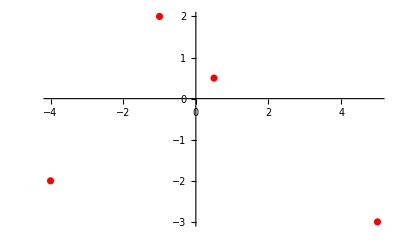

```mathematica
ListPlot[{{5,-3},{1/2,1/2},{-1,2},{-4,-2}},PlotStyle->{Red}]
```

( b ) Calcular :  z_1 =  z 1_(π/2),     w_1= w 1_((3π)/2) ,  s_1 = s 1_π,   j_1 =  j 1_(π/4)

Encontramos números que se encuentran en forma polar y otros en forma binómica, para poder multiplicar números complejos debemos tener ambos factores en la misma forma.

Opción 1. Pasamos los números complejos z, w, s y j a su forma polar

| z |=√(5^2+(-3)^2)=√36=6
Arg(z)=Arctg(-3/5)

| w |=√((1/2)^2+(1/2)^2)=1/(√2)
Arg(w)=Arctg((1/2)/(1/2))=Arctg(1)=π/4

| s |=√((-1)^2+2^2)=√5
Arg(s)=Arctg(2/-1)

| j |=√((-4)^2+(-2)^2)=√20=2 √5
Arg(j)=Arctg(-2/-4)

z_1=z*1_(π/2)=(5-3ⅈ)1_(π/2)=

## 14.- Resolver la ecuación z^3 + 8 ⅈ = 0

Solución :

z^3  + 8 ⅈ = 0 ⟹ z^3  = -8 ⅈ 
Las soluciones serán las raíces cúbicas de -8 ⅈ. 
Comenzaremos expreseando el número complejo en forma polar, ya que por comodidad es más sencillo trabajar con esta forma del número complejo, para ello debemos de calcular previamente su módulo y su argumento.

Módulo=√(0^2+(-8)^2)=8
Argumento. Tenemos un número con parte real 0 e imaginaria -8, es decir, es un número cuyo afijo se sitúa en la parte negativa del eje de ordenadas, por lo que su argumento es de (3π)/2+2πκ

Así -8 ⅈ=8_((3π)/2+2πk)

Una vez tenemos el número es su forma polar, las raíces cúbicas se obtienen haciendo la raíz cúbica del modulo y dividiendo el argumento en tres partes. Al tratarse de la raíz cúbica se obtendrán tres raíces (una para cada k=0,1,2).

Luego,
z_0=(8^(1/3))_(((3π)/2+2π·0)/3)=2_(π/2)  ⟹z_0=2(Cos(π/2)+ⅈSen(π/2))=2(0+ⅈ)=2ⅈ
z_1=(8^(1/3))_(((3π)/2+2π·1)/3)=2_(π/2+(2π)/3)=2_((7π)/6)  ⟹z_1=2(Cos((7π)/6)+ⅈSen((7π)/6))=2(-(√3)/2-1/2 ⅈ)=-√3-ⅈ
z_2=(8^(1/3))_(((3π)/2+2π·2)/3)=2_(π/2+(4π)/3)=2_((11π)/6)  ⟹z_2=2(Cos((11π)/6)+ⅈSen((11π)/6))=2((√3)/2-1/2 ⅈ)=√3-ⅈ

 Estas serían las 3 soluciones de la ecuación.

Con Mathematica,

```mathematica
Reduce[z^3  + 8 ⅈ==0,z]
```

z==2 ⅈ||z==-ⅈ-√3||z==-ⅈ+√3

## 15.- Resolver la ecuación ( 1 + ⅈ ) z^3 - 2ⅈ = 0

Solución :

( 1 + ⅈ ) z^3 - 2ⅈ = 0 ⟹ z^3  = (2 ⅈ)/(1+ⅈ)=(2 ⅈ)/(1+ⅈ)·(1- ⅈ)/(1-ⅈ)=(2+2i)/2=1+ⅈ 

Las soluciones serán las raíces cúbicas de 1+ⅈ. 
Comenzaremos expresando el número complejo en forma polar, ya que por comodidad es más sencillo trabajar con esta forma del número complejo, para ello debemos de calcular previamente su módulo y su argumento.

Módulo=√(1^2+(1)^2)=√2
Argumento. Tenemos un número con parte real 1 e imaginaria 1, se trata de un número complejo cuyo punto afijo se encuentra en el primer cuadrante. Es más, al ser (1,1) se trata de la bisectriz del primer cuadrante, por lo que su argumento es de π/4+2πκ

Así 1+ⅈ=(√2)_(π/4)

Una vez tenemos el número es su forma polar, las raíces cúbicas se obtienen haciendo la raíz cúbica del modulo y dividiendo el argumento en tres partes. Al tratarse de la raíz cúbica se obtendrán tres raíces (una para cada k=0,1,2).

Luego,
z_0=((√2)^(1/3))_((π/4+2π·0)/3)=(2^(1/6))_(π/12)  ⟹z_0=2^(1/6)(Cos(π/12)+ⅈSen(π/12))=2^(1/6)((1+√3)/(2 √2)+(-1+√3)/(2 √2)ⅈ)=(1+√3)/(2 2^(1/3))+(-1+√3)/(2 2^(1/3))ⅈ
z_1=((√2)^(1/3))_((π/4+2π·1)/3)=(2^(1/6))_(π/4+(2π)/3)=(2^(1/6))_((3 π)/4)  ⟹z_1=2^(1/6)(Cos((3 π)/4)+ⅈSen((3 π)/4))=2^(1/6)(-1/(√2)+1/(√2)ⅈ)=-1/2^(1/3)+1/2^(1/3)ⅈ
z_2=((√2)^(1/3))_((π/4+2π·2)/3)=(2^(1/6))_(π/4+(4π)/3)=(2^(1/6))_((17 π)/12)  ⟹z_2=2^(1/6)(Cos((17 π)/12)+ⅈSen((17 π)/12))=2^(1/6)(-(-1+√3)/(2 √2)-(1+√3)/(2 √2)ⅈ)=-(-1+√3)/(2 2^(1/3))-(1+√3)/(2 2^(1/3))ⅈ

 Estas serían las 3 soluciones de la ecuación.

Con Mathematica,

```mathematica
Reduce[(1+ⅈ)z^3 -2ⅈ==0,z]//ComplexExpand
```

z==1/(2 2^(1/3))+(√3)/(2 2^(1/3))+ⅈ (-1/(2 2^(1/3))+(√3)/(2 2^(1/3)))||z==1/(2 2^(1/3))-(√3)/(2 2^(1/3))+ⅈ (-1/(2 2^(1/3))-(√3)/(2 2^(1/3)))||z==-(1-ⅈ)/2^(1/3)

## 16.- Hallar todas las soluciones de la ecuación ( z^2 - 7 ) ( z^3 +ⅈ ) = 0

Solución :

( z^2 - 7 ) ( z^3 +ⅈ )  = 0 ⟹ {z^2-7=0
z^3+ⅈ=0 ⟹ {z=±√7
z=-i^(1/3)

Tenemos por un lado dos raíces reales: √7 y -√7 y por otro lado tres soluciones complejas que serán las raíces cúbicas de -ⅈ. 
Comenzaremos expresando el número complejo en forma polar, ya que por comodidad es más sencillo trabajar con esta forma del número complejo, para ello debemos de calcular previamente su módulo y su argumento.

Módulo=√(0^2+(-1)^2)=1
Argumento. Tenemos un número con parte real 0 e imaginaria -1, se trata de un número complejo cuyo punto afijo se encuentra en el semieje de coordenadas negativo. Por lo que su argumento es de (3π)/2+2πκ

Así -ⅈ=1_((3π)/2)

Una vez tenemos el número es su forma polar, las raíces cúbicas se obtienen haciendo la raíz cúbica del modulo y dividiendo el argumento en tres partes. Al tratarse de la raíz cúbica se obtendrán tres raíces (una para cada k=0,1,2).

Luego,
z_0=(1^(1/3))_(((3π)/2+2π·0)/3)=1_(π/2)  ⟹z_0=1(Cos(π/2)+ⅈSen(π/2))=0+ⅈ=ⅈ
z_1=(1^(1/3))_(((3π)/2+2π·1)/3)=1_(π/2+(2π)/3)=2_((7π)/6)  ⟹z_1=1(Cos((7π)/6)+ⅈSen((7π)/6))=-(√3)/2-1/2 ⅈ
z_2=(1^(1/3))_(((3π)/2+2π·2)/3)=1_(π/2+(4π)/3)=2_((11π)/6)  ⟹z_2=1(Cos((11π)/6)+ⅈSen((11π)/6))=(√3)/2-1/2 ⅈ

 Estas serían las 3 soluciones complejas de la ecuación.

Con Mathematica,

```mathematica
Reduce[(z^2-7) (z^3+ⅈ)==0,z]
```

z==ⅈ||z==-√7||z==√7||z==1/2 (-ⅈ-√3)||z==1/2 (-ⅈ+√3)